## Oscillator disturbance rejection for uncertain frequency using optimal PD control (Problem 9.4)

```mathematica
Clear["Global`*"];
```

```mathematica
eqs={x''[t]+ω^2 x[t]==u[t],u[t]==-Kp x[t]-Kd D[x[t],t], x[0]==0,x'[0]==1};
{xs,us}=DSolveValue[eqs,{x[t],u[t]},t,Assumptions->{Kd>0,Kp>0,ω>0,Kd^2-4 (Kp+ω^2)<0}]//FullSimplify ;  TraditionalForm[{xs,us}]
```

{(2 ⅇ^(-(Kd t)/2) sin(1/2 t √(4 (Kp+ω^2)-Kd^2)))/(√(4 (Kp+ω^2)-Kd^2)),ⅇ^(-(Kd t)/2) (((Kd^2-2 Kp) sin(1/2 t √(4 (Kp+ω^2)-Kd^2)))/(√(4 (Kp+ω^2)-Kd^2))-Kd cos(1/2 t √(4 (Kp+ω^2)-Kd^2)))}

Both over- and underdamped responses give same functional form for cost function j, so the form given here applies to be both cases, with Cos → Cosh, etc. for the overdamped case.

Also:  time has been scaled so that ω_0=1.

```mathematica
J=Integrate[1/2(xs^2+ us^2),{t,0,∞},Assumptions->{ω>0,Kd>0,Kp>0,Kd^2-4 (Kp+ω^2)<0}]//Simplify
```

(Kd^2+(1+Kp^2)/(Kp+ω^2))/(4 Kd)

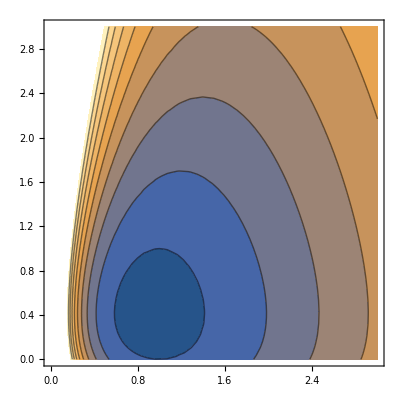

```mathematica
ContourPlot[J/.{ω->1},{Kd,0,3},{Kp,0,3}]
```

```mathematica
{{Kd0,Kp0}={Kd,Kp}/.Solve[{D[J, Kd]==0,D[J, Kp]==0},{Kd,Kp}][[4]]/.ω->1//Simplify, {Kd0,Kp0,J/.{ω->1,Kd->Kd0,Kp->Kp0}}//N}
```

{{√(2 (-1+√2)),-1+√2},{0.91018,0.414214,0.45509}}

```mathematica
J0=J/.{ω->1,Kd->Kd0,Kp->Kp0}//Simplify
```

√(-1/2+1/(√2))

Introduce scaled quantities

```mathematica
{j=1/J0 J/.{Kd->kd Kd0,Kp->kp Kp0}//FullSimplify,j/.{ω->1,kd->1,kp->1}}//Simplify
```

{((1+√2) (2 (-1+√2) kd^2+(1+(3-2 √2) kp^2)/((-1+√2) kp+ω^2)))/(4 kd),1}

```mathematica
Collect[j,kd,Simplify]
```

kd/2+(1+√2+(-1+√2) kp^2)/(4 kd ((-1+√2) kp+ω^2))

```mathematica
bvec=Grad[D[j, ω, ω],{kd,kp}]/.{ω->1,kd->1,kp->1}//Simplify;  
ahess=D[j,{{kd,kp},2}]/.{ω->1,kd->1,kp->1}//Simplify;MatrixForm /@ {bvec,ahess}
```

{(-2+1/(√2)
-9/2+5/(√2)),(1 | 0
0 | 1/4 (2-√2))}

```mathematica
{dkvec=-1/2 Inverse[ahess].bvec//Simplify;  dkvec//MatrixForm,dkvec//N}
```

{(1-1/(2 √2)
4-1/(√2)),{0.646447,3.29289}}

Series expansions

```mathematica
js=Series[j/.{ω->1+ϵ, kd->1+dkvec[[1]] ϵ^2,kp->1+dkvec[[2]] ϵ^2},{ϵ,0,4}]//Simplify//Normal
```

1-ϵ/(√2)+(1-1/(2 √2)) ϵ^2+7/4 (-1+√2) ϵ^3+1/16 (-55+29 √2) ϵ^4

```mathematica
js1=1+(1-1/(2 √2)) ϵ^2+1/16 (-55+29 √2) ϵ^4;
```

check by numerical evaluation of j with lognormal a

```mathematica
μ=-1/2 Log[1+ϵ^2];σ=√Log[1+ϵ^2];Jexp[e_,KKd_,KKp_] :=NExpectation[J/.{Kd->KKd,Kp->KKp},ω\[Distributed]LogNormalDistribution[μ/.ϵ->e,σ/.ϵ->e]]
```

```mathematica
de=0.04;      (* increment for computing data *)
JKmin[ϵ_]:=FindMinimum[Jexp[ϵ,Kd,Kp],{{Kd,Kd0},{Kp,Kp0}}];
JKstar=Table[{ϵ,JKmin[ϵ]},{ϵ,0.01,1,de}]//Flatten;
αstar=JKstar[[1;;;;4]];Jstar=JKstar[[2;;;;4]]; Kstar=JKstar[[3;;;;4]] /.(_->e_)->e; Kpstar=JKstar[[4;;;;4]] /.(_->e_)->e;
Jnaive=Table[Jexp[ϵ,Kd0,Kp0],{ϵ,0.01,1,de}];
Jpert=Table[Jexp[ϵ,Kd1,Kp1],{ϵ,0.01,1,de}];

Jlist=Transpose[{αstar,Jstar}]; Klist=Transpose[{αstar,Kstar}]; 
Kplist=Transpose[{αstar,Kpstar}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
Kd1=Kd0(1+dkvec[[1]] ϵ^2);Kp1=Kp0(1+dkvec[[2]] ϵ^2);
p0=Plot[{Jexp[ϵ,Kd0,Kp0],Jexp[ϵ,Kd1,Kp1]},{ϵ,0.01,1}];
```

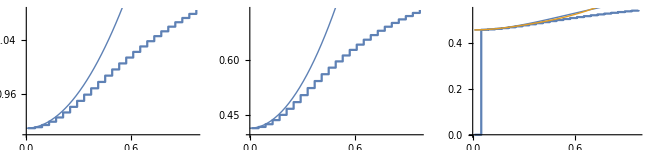

```mathematica
GraphicsRow[{Show[ListPlot[Klist],Plot[Kd1,{ϵ,0,1}]],Show[ListPlot[Kplist],Plot[Kp1,{ϵ,0,1}]],Show[ListPlot[Jlist],p0]},ImageSize->{650,150},AspectRatio->Full]
```

Export data

```mathematica
dat=Transpose[{αstar,Jstar,Jnaive,Jpert,Kstar,Kpstar}];

(* 
SetDirectory[NotebookDirectory[]];
Export["oscKshiftPD.dat",dat]; 
*)
```